```mathematica
ASTOR PRIETO DEHGHANPOUR
```

# Pràctica 12: Arbres i arbres generadors

En aquesta pràctica continuarem utilitzant la llibreria Combinatorica`.

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Algorisme de Hierholzer  (Grafs Eulerians)

Donat un graf eulerià G, aquest algorisme serveix per  trobar un cicuit eulerià. 

L’algorisme de Hierholzer es basa en el resultat següent:

Teorema: 
Un graf connex G és eulerià si i només si s'expressa com  una unió de cicles sense arestes en comú. 

En aquest cas, el cicle eulerià s’obté empalmant tots els cicles de manera convenient. 

Anem a programar aquest algoritme. Per fer-ho dividirem el programa en dues parts. En la primera part calculem els cicles disjunts que componen el graf:

```mathematica
cycEu[G_]:=
Module[{ Z,R={},G1},
G1=G;
Z=FindCycle[G1];
While[Z≠ {},
G1=DeleteCycle[G1,Z];
R=Append[R,Z];
Z=FindCycle[G1];
];
R
]
```

Per exemple, si considerem el següent graf eulerià:

```mathematica
G1=FromAdjacencyLists[{{2,3,4,5},{1,3,4,5},{1,2,4,5},{1,2,3,5},{1,2,3,4,6,7},{5,7},{5,6}}]
```

⁃Graph:<13,7,Undirected>⁃

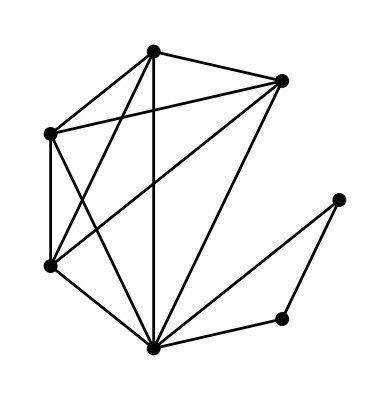

```mathematica
ShowLabeledGraph[G1]
```

```mathematica
cycEu[G1]
```

{{3,1,2,3},{5,1,4,2,5},{5,3,4,5},{7,5,6,7}}

En la segona part empalmem els cicles de manera convenient per obtenir un cicle eulerià. Es comença per un cicle qualsevol i es van empalmant la resta de cicles, un cicle cada vegada, de manera que el resultat és un circuit sense arestes repetides.

```mathematica
euleria[cycles_]:=Module[{cyc,euler,c,v},
{euler,cyc}={First[cycles],Rest[cycles]};
  While[Length[cyc]>0,
                         c=First[Select[cyc,(Intersection[euler,#]=!={})&]];
                         v=First[Intersection[euler,c]];
                         euler=Join[ RotateLeft[c,Position[c,v][[1,1]]],RotateLeft[euler,Position[euler,v][[1,1]]]];
                   cyc=Complement[cyc,{c}]];AppendTo[euler,euler[[1]]]]
```

```mathematica
euleria[cycEu[G1]]
```

{6,7,7,5,5,3,3,1,4,2,5,5,1,2,3,4,5,6}

Compareu el resultat anterior amb la solució que dóna la comanda EulerianCycle. Quines són les diferéncies?

```mathematica
Exercici: Trobeu un circuit eulerià del graf  G2 següent.
```

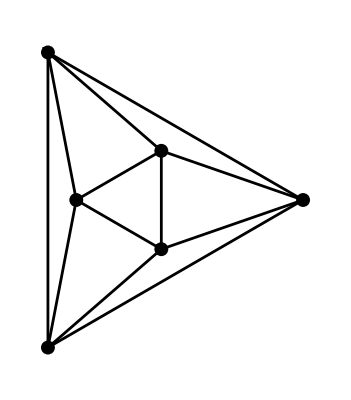

```mathematica
G2=FiniteGraphs[[16]];
ShowLabeledGraph[G2]
```

```mathematica
euleria[cycEu[G2]]
```

{5,6,6,4,2,5,3,6,6,1,2,3,3,1,4,5}

Arbres

Definició: Una aresta d’un graf connex s’anomena aresta pont si al suprimir-la el graf resultant no és connex. 
Un arbre és un graf connex on totes les arestes són arestes pont. 

Per caracteritzar els arbres tenim els següents resultats:

               Teorema: 
Un graf G connex  és un arbre si i només |V|-|E|=1, on |V| és el nombre de vèrtexs  i  |E| el  d'arestes.

               Teorema: 
Un graf G connex és un arbre si i només si no conté cap cicle.


La següent comanda ens diu si un graf és un arbre:

```mathematica
?TreeQ
```

RowBox[{"TreeQ", "[", StyleBox["g", "TI"], "]"}] yields True if graph g is a tree.

Per exemple:

```mathematica
Ar3={{1,2},{1,4},{1,6},{2,3},{4,5}}
```

{{1,2},{1,4},{1,6},{2,3},{4,5}}

```mathematica
G3=FromUnorderedPairs[Ar3]
```

⁃Graph:<5,6,Undirected>⁃

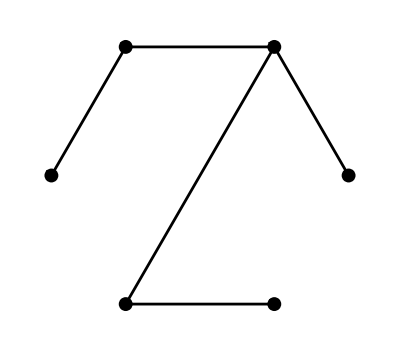

```mathematica
ShowLabeledGraph[G3]
```

```mathematica
TreeQ[G3]
```

True

```mathematica
?TreeGraph
```

TreeGraph[{v_1,v_2,…},{u_1,u_2,…}] yields a tree where u_i is the predecessor of v_i.
TreeGraph[{e_1,e_2,…}] yields a tree with edges e_j.
TreeGraph[{v_1,v_2,…},{e_1,e_2,…}] yields a tree with vertices v_i and edges e_j.
TreeGraph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a tree with vertex and edge properties defined by the symbolic wrappers w_k.

Per exemple:

```mathematica
G7=TreeGraph[{{1,2},{2,3},{1,4},{3,5},{3,6}}]
```

-Graphics-

Exercici: Calculeu la diferència |V|-|E| dels grafs següents i digueu si són arbres. En cas afirmatiu, dibuixeu l’arbre amb la comanda TreeGraph. En cas negatiu, trobeu una aresta que no sigui pont i un cicle de l’arbre.

{{1,2},{1,4},{1,6},{2,3},{4,5},{5,1}}

⁃Graph:<6,6,Undirected>⁃

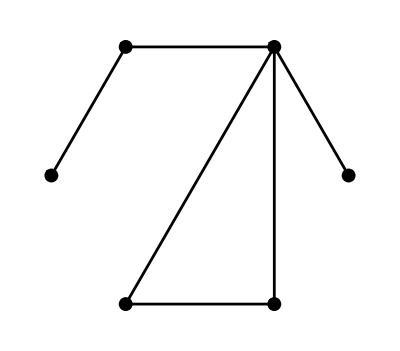

```mathematica
Ar4={{1,2},{1,4},{1,6},{2,3},{4,5},{5,1}}
G4=FromUnorderedPairs[Ar4]
ShowLabeledGraph[G4]
```

```mathematica
TreeGraph[Edges[G4]]
```

TreeGraph[{{1,2},{1,4},{1,6},{2,3},{4,5},{1,5}}]

```mathematica
TreeQ[G4]
```

False

```mathematica
LLA5={{2,3,4},{1,5,10,11},{1,8,9,10},{1,6,7},{2},{4},{4},{3},{3},{2,3},{2,12},{11}}
```

{{2,3,4},{1,5,10,11},{1,8,9,10},{1,6,7},{2},{4},{4},{3},{3},{2,3},{2,12},{11}}

```mathematica
G5=FromAdjacencyLists[LLA5]
```

⁃Graph:<12,12,Undirected>⁃

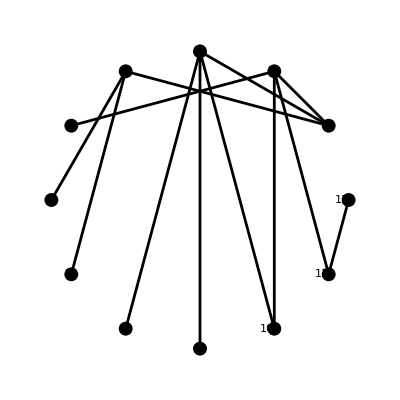

```mathematica
ShowLabeledGraph[G5]
```

```mathematica
TreeGraph[Edges[G5]]
```

TreeGraph[{{1,2},{1,3},{1,4},{2,5},{2,10},{2,11},{3,8},{3,9},{3,10},{4,6},{4,7},{11,12}}]

```mathematica
TreeQ[G5]
```

False

```mathematica
LLA6={{2,3,4},{1,5,11},{1,8,9,10},{1,6,7},{2},{4},{4},{3},{3},{3},{2,12},{11}}
```

{{2,3,4},{1,5,11},{1,8,9,10},{1,6,7},{2},{4},{4},{3},{3},{3},{2,12},{11}}

```mathematica
G6=FromAdjacencyLists[LLA6]
```

⁃Graph:<11,12,Undirected>⁃

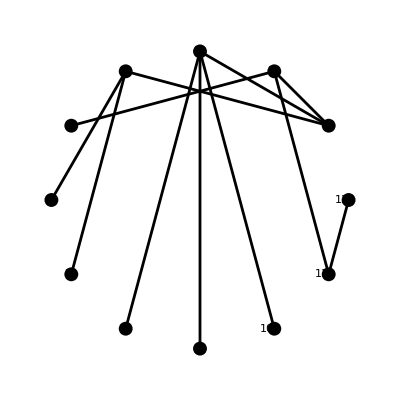

```mathematica
ShowLabeledGraph[G6]
```

```mathematica
TreeGraph[Edges[G6]]
```

-Graphics-

```mathematica
TreeQ[G6]
```

True

Exercici: Construiu un graf que sigui un arbre i un altre que no ho sigui.

```mathematica
LLA6 = {{2,3},{4,5},{6,7},{2},{2},{3},{3}}
```

{{2,3},{4,5},{6,7},{2},{2},{3},{3}}

```mathematica
G7 = FromAdjacencyLists[LLA6]
```

⁃Graph:<6,7,Undirected>⁃

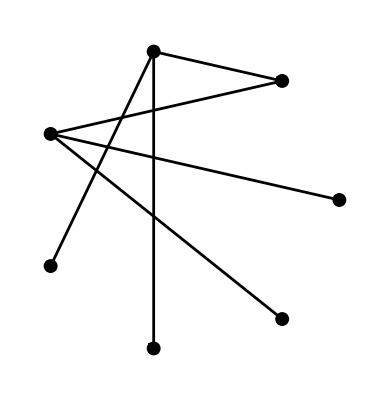

```mathematica
ShowLabeledGraph[G7]
```

```mathematica
TreeQ[G7]
```

True

```mathematica
TreeGraph[Edges[G7]]
```

-Graphics-

### Arbres generadors:

Definició: Sigui G un graf, direm que un subgraf  T de G és un arbre generador si T és un arbre i conté tots els vèrtexs de G.

Per exemple, si considerem el següent graf

```mathematica
G91=FromAdjacencyLists[{{2,3},{1,3,4},{1,2,4,5},{2,3,5},{3,4}}]
```

⁃Graph:<7,5,Undirected>⁃

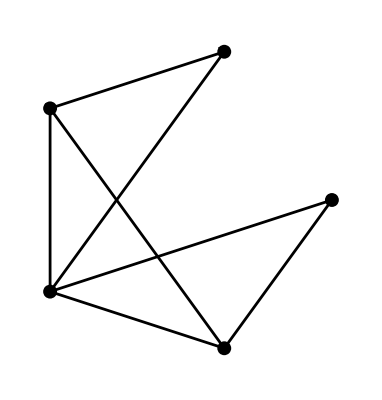

```mathematica
ShowLabeledGraph[G91]
```

Un arbre del graf és:

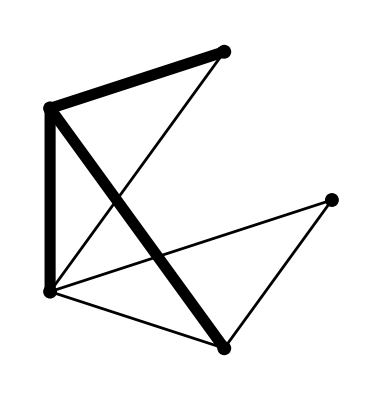

```mathematica
ShowGraph[G91,{{{1,2},{2,3},{2,4},EdgeStyle->Thick}},VertexNumber->True]
```

Exercici:  És  T={{1,2},{2,3},{2,4}} un arbre generador de G91?, per qué?. 

	Falta el vertex 5 al arbre per a que sigui Arbre Generador. 

Mostrem a continuació un  arbre generador de G91:

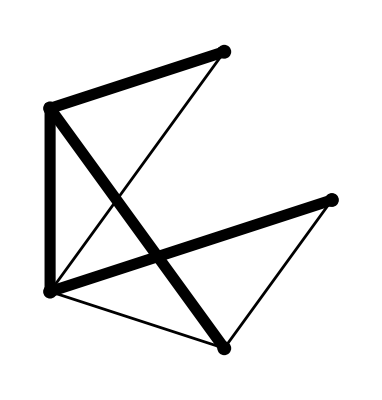

```mathematica
ShowGraph[G91,{{{1,2},{2,3},{2,4},{3,5},EdgeStyle->Thick}},VertexNumber->True]
```

El resultat següent és molt important.

                                   Teorema: 
Tot graf connex conté algun arbre generador. 

Observació: Un graf pot tenir més d'un arbre generador. 

A continuació presentem un algorisme que troba un arbre generador d’un graf connex donat.

Construïm un arbre T:  Comencem l’arbre amb el vèrtex 1 i hi afegim totes les arestes del graf G incidents amb el vèrtex 1: {1, v_1},.....{1, v_n}. Per cada un dels nous vèrtexs v_i farem el mateix però sense afegir arestes que l'uneixin a vèrtexs que ja són de l'arbre T. D'aquesta manera evitem crear cicles. S’acaba quan T conté tots els vèrtexs de G. 

A continuació es detalla l'algorisme explicat anteriorment. La llista L  conté els vèrtexs de l'arbre (en cada pas) als quals s'han d'afegir arestes. A la llista T hi anem afegint les arestes de l'arbre generador. La llista Vi va acumulant els vèrtexs ja visitats.

Inicialitzar L={1},T={} i Vi={1}
Mentres L≠{}:
	l⟵primer element de L,
	VN⟵Veins de l que no apareixen a Vi,
	afegir a T les arestes {l,v} per tot v de VN,
	eliminar l de L i afegir-hi VN,
	afegir VN a Vi
Escriure T.

Implementem l'algorisme anterior a partir de la taula d'adjacències.

```mathematica
MaxTree[G_]:=
Module[{L={1}, T={}, Vi={1},VN={},i,l},
While[L ≠ {},
l=L[[1]];
VN=Complement[ToAdjacencyLists[G][[l]],Vi];
L=Drop[L,1];
For [i=1,i≤Length[VN],i++,T=Append[T,{l,VN[[i]]}]; L=Append[L,VN[[i]]];Vi=Append[Vi,VN[[i]]];];
];TreeGraph[T,VertexLabels->"Name"]]
```

Exercici: Trobeu un arbre generador dels grafs següents:

```mathematica
G10=FiniteGraphs[[1]]
G11=FiniteGraphs[[2]]
```

⁃Graph:<24,12,Undirected>⁃

⁃Graph:<42,28,Undirected>⁃

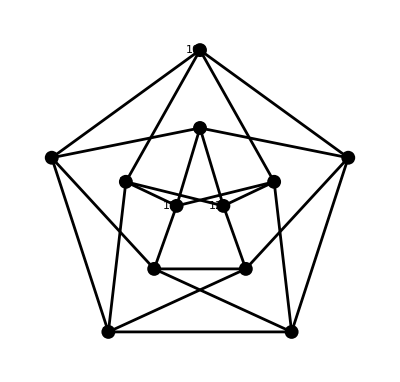

```mathematica
ShowLabeledGraph[G10]
```

```mathematica
ToAdjacencyLists[G10]
```

{{7,10,11,12},{3,6,8,11},{2,7,9,12},{8,10,11,12},{6,9,11,12},{2,5,7,10},{1,3,6,8},{2,4,7,9},{3,5,8,10},{1,4,6,9},{1,2,4,5},{1,3,4,5}}

```mathematica
MaxTree[G10]
```

-Graphics-

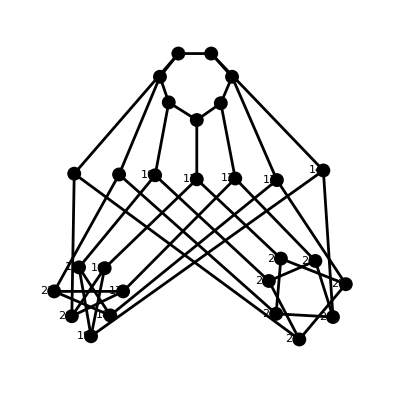

```mathematica
ShowLabeledGraph[G11]
```

```mathematica
ToAdjacencyLists[G11]
```

{{2,3,8},{1,5,14},{1,4,9},{3,7,10},{2,6,13},{5,7,12},{4,6,11},{1,20,25},{3,21,24},{4,15,23},{7,16,22},{6,17,28},{5,18,27},{2,19,26},{10,18,19},{11,19,20},{12,20,21},{13,15,21},{14,15,16},{8,16,17},{9,17,18},{11,24,27},{10,25,28},{9,22,26},{8,23,27},{14,24,28},{13,22,25},{12,23,26}}

```mathematica
MaxTree[G11]
```

-Graphics-

### Funció de cost. Arbres generadors de mínim cost. Algoritme de Kruskal.

Definició: Un graf G direm que és ponderat si  a cada aresta e del graf se li assigna un nombre no negatiu w(e), que anomenarem pes (o cost)  de l’aresta e.
El pes d’un graf  és la suma dels pesos de les arestes que defineixen el graf. Anàlogament, el pes d’un recorregut  és la suma dels pesos de les arestes que defineixen el recorregut.

Per definir grafs ponderats amb el Mathematica ho farem de la manera següent:
En primer lloc definim el graf de manera habitual a partir de les seves arestes

```mathematica
G12=FromUnorderedPairs[{{1,2},{2,3},{1,4},{4,3},{4,5},{3,5}}]
```

⁃Graph:<6,5,Undirected>⁃

A continuació introduim la funció de pesos

```mathematica
W=SetEdgeWeights[G12,{2,2,5,8,1,3}]
```

⁃Graph:<6,5,Undirected>⁃

Per visualitzar-lo:

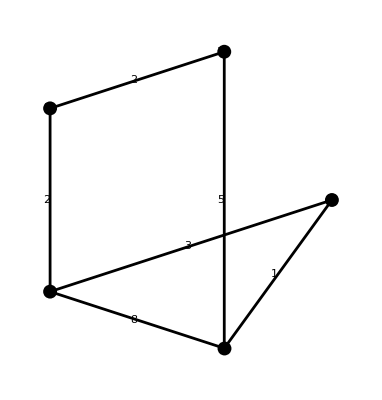

```mathematica
ShowLabeledGraph[SetEdgeLabels[W,GetEdgeWeights[W]]]
```

Un arbre generador de mínim pes (o mínim cost) és un arbre generador de manera que el seu pes és mínim d’entre tots els arbres generadors possibles. Anem a programar això implementant l’algorisme de Kruskal.

                                             Algorisme de Kruskal 
Entrem el graf ponderat G=(V,E,w)
Inicialitzem: T ={},  E'=E. 
Mentre  nombre d'arestes de T < n-1 
fer 
e=aresta de pes mínim de  E' ;
E'=E'-e; 
       Si  T+e no conté cap cicle
              T=T+e
        fi Si
fi Mentre  

Amb aquest algorisme a cada iteració triem l’aresta de pes mínim d’una llista d’arestes ponderades.
Per facilitar aquesta elecció, abans d’introduir la llista l’ ordenarem respecte del pes amb la següent instrucció.

```mathematica
W13={{{1,2},2},{{2,3},2},{{1,4},5},{{4,3},8},{{4,5},1},{{3,5},3}}
```

{{{1,2},2},{{2,3},2},{{1,4},5},{{4,3},8},{{4,5},1},{{3,5},3}}

```mathematica
G13 = {{1,2},{2,3},{1,4},{4,3},{4,5},{3,5}}
```

{{1,2},{2,3},{1,4},{4,3},{4,5},{3,5}}

```mathematica
G13 = FromUnorderedPairs[G13]
```

⁃Graph:<6,5,Undirected>⁃

```mathematica
W13=Sort[W13,(#1[[2]]≤#2[[2]])&]
```

{{{4,5},1},{{1,2},2},{{2,3},2},{{3,5},3},{{1,4},5},{{4,3},8}}

```mathematica
e=Table[W13[[i,1]],{i,1,Length[W13]}]
```

{{4,5},{1,2},{2,3},{3,5},{1,4},{4,3}}

Una possible implementació de l’algorisme és

```mathematica
Krus[w_,n_]:=
Module[{ T={},e,nw,wT={},we,G,G1,GT},
nw=w;
While[Length[T]< n-1,
               e=nw[[1,1]];
         we=nw[[1,2]];
               nw=Delete[nw,1];
        If [AcyclicQ[FromUnorderedPairs[Append[T,e]]]==True,
                      T=Append[T,e];wT=Append[wT,we]]];
G1=FromUnorderedPairs[Table[w[[i,1]],{i,1,Length[w]}]]; G=SetEdgeWeights[G1,Table[w[[i,2]],{i,1,Length[w]}]];
GT=SetEdgeWeights[FromUnorderedPairs[T],wT];
{ShowLabeledGraph[SetEdgeLabels[GT,GetEdgeWeights[GT]]],ShowLabeledGraph[SetEdgeLabels[G,GetEdgeWeights[G]]]}]
```

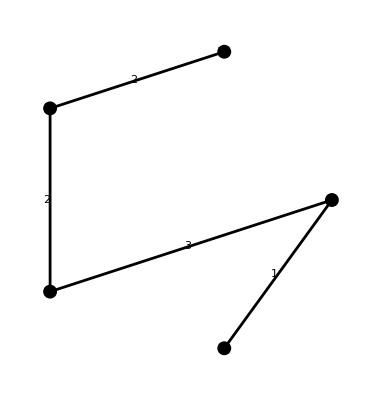
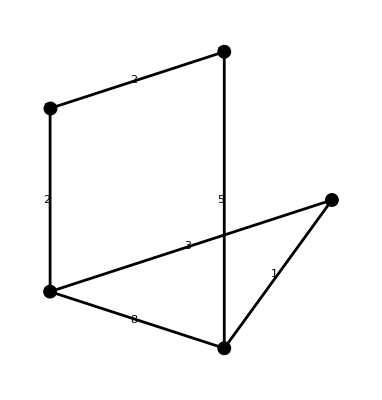

```mathematica
Krus[W13,5]
```

En Mathematica això també es pot fer amb la comanda:

```mathematica
?MinimumSpanningTree
```

MinimumSpanningTree[g] uses Kruskal's algorithm to find a minimum spanning tree of graph g.

Aquesta comanda serveix per grafs ponderats i grafs no no ponderats. Si considerem el graf anterior:

```mathematica
WG=SetEdgeWeights[G13,{2,2,5,8,1,3}]
```

⁃Graph:<6,5,Undirected>⁃

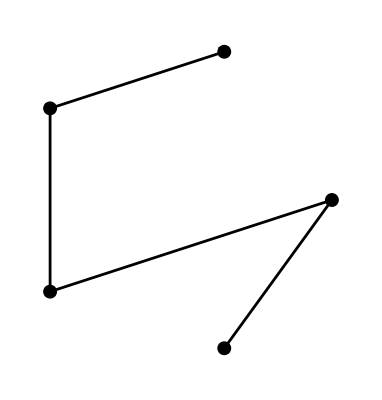

```mathematica
ShowLabeledGraph[MinimumSpanningTree[WG]]
```

### EXERCICI PER TRAMETRE

Trobeu un arbre generador de mínim pes per al següent graf:

```mathematica
G14=FromUnorderedPairs[{{1,2},{1,4},{2,4},{4,5},{4,6},{5,6},{2,6},{2,3},{3,6},{3,7},{6,7}}]
```

⁃Graph:<11,7,Undirected>⁃

```mathematica
w14={5,5,5,3,3,1,3,5,4,2,5}
```

{5,5,5,3,3,1,3,5,4,2,5}

```mathematica
WG14=SetEdgeWeights[G14,w14]
```

⁃Graph:<11,7,Undirected>⁃

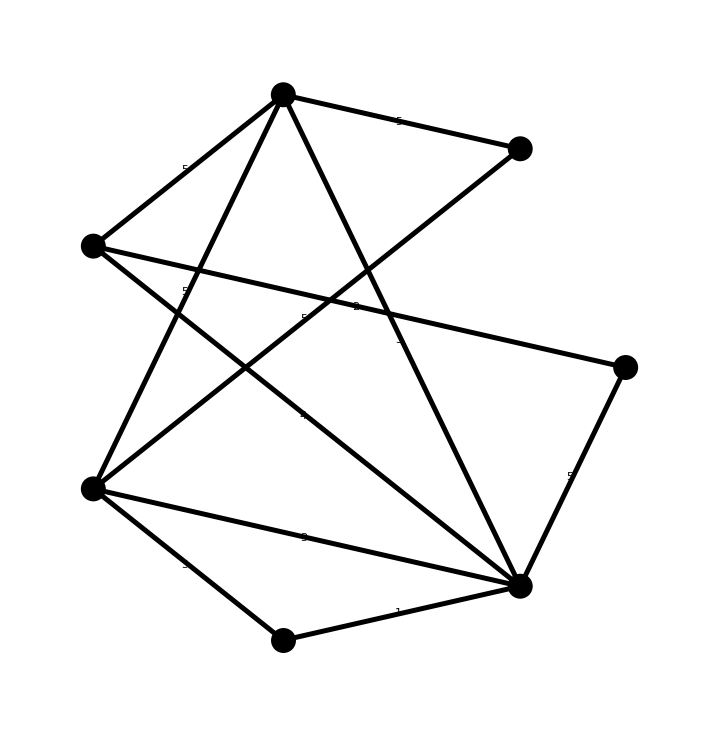

```mathematica
RR = MinimumSpanningTree[WG14]
```

⁃Graph:<6,7,Undirected>⁃

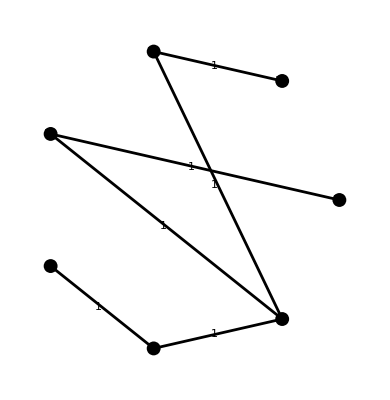

```mathematica
ShowLabeledGraph[SetEdgeLabels[RR,GetEdgeWeights[RR]]]
```

```mathematica
TreeGraph[Edges[RR]]
```

-Graphics-